# Project report

## SFC×GC recommissioning

D Malan

Department of Chemistry
University of Pretoria

16 December 2019

## Introduction

The aim of this project is to get the SFC×GC into a running state.

## Experimental

### Coaxial heater

The coaxial heater assembly was removed without undue difficulty.

### GC

The Varian 3300 started up OK, with no more than the normal number of errors. I set the temperature limits to 400 °C, but I think I forgot to actually set the inlet and detector temperatures. I normally set them to 350 °C, but when I investigated trouble I found the the inlet was still cool. I took the opportunity to change the septum. The GC heated up normally. I’d forgotten how slow a process this was. 
The FID started normally.

To test the GC I set the column temperature to 250 °C and injected a  few microlitres of methanol. This did not give any signal on the FID. Squirting methanol vapour into the FID gave a strong and rapid response. The leak tester did not show any hydrogen leak at the detector end of the column. There seemed to be a slight leak at the inlet end, but at an ambiguous rate. Not as slow as is sometimes seen at a screw thread leak, but not as fast as usual on a broken column. At the cryo-coolant outlet however, there was a significant amount of hydrogen, indicating  a large flow caused by a serious leak. I concluded that the column had broken inside the coaxial heater.

### Capillary column fracture

I removed the coaxial heater from the Varian, and took it to the bench. It came out normally, although I had to hammer out about half of the cartridge heaters. This shows that the manifold blocks keep distorting when heated.

In my thesis I'd said that I’d never seen a column failure because of thermal shock or thermal fatigue, and I worried that I’d have to eat my words. On examining the column after I’d removed it from the heater, it seemed that the column and the tip of the ferrule had overheated. This left the capillary fragile, and it broke under normal operating conditions.

The figure below shows that the one end of the ferrule is blackened, possibly by heat. The other end is still shiny.

The colours of the column seems to indicate that the inlet end got hotter than the detector end, and that got hotter than the column itself. That the ends of the column were exposed to higher heat for longer periods of time is not surprising: the manifolds blocks are kept constantly at a higher temperature than the column, and quite a lot higher. I maintain them at about 350 °C.

I picked representative colours from the image above using the Mathematica index tool.

```mathematica
colors ={{190,139,120},{150,123,102},{179,136,117}}
```

{{190,139,120},{150,123,102},{179,136,117}}

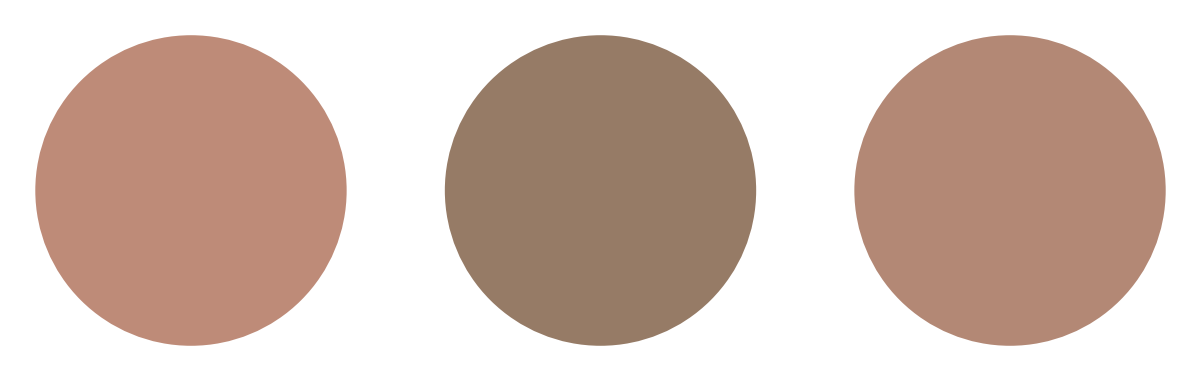

```mathematica
GraphicsGrid[{Graphics[{RGBColor@@(#/255), Disk[]}]&/@ colors}]
```

It is obvious that the middle disk is darker than the other two: this represents the inlet end, in the middle of the photograph above. 

It also seems as if the column was burned more towards the end. I don’t know why this would be. That would seem to indicate a temperature gradient from top to bottom along the manifold block.

Because it is not clear when this overheating happened, there is not much I can do to prevent it from happening again. I will try to keep the temperatures lower and not switch on the heaters unless necessary.

### Column re-installation

The installation of the new column went without incident. I noticed that the inlet is less rigidly mounted than I thought. This might cause relative movement between the inlet stem and the manifold block, risking the column breaking. I wedged the inlet it into one position. The inlet is now not very parallel with the rails, so during a future installation it would be a good idea to adjust them.  
I forgot to remove the plastic protection clips, so when the manifold blocks started heating up they melted. In a panicked attempt to removed them,  the coaxial heater touched the oven floor and heated red hot. There is now a hydrogen leak inside the coaxial heater, so the column must have fractured.

## Conclusion

I  have created a column installation checklist on Evernote, and used to use it. However, because I found Evernote to be irritatingly slow I no longer use it regularly. It has also been a while since I last installed a column. This means that I did not think of using the checklist, which would have reminded me to remove the plastic protection clips.

The last job of the column installation is to solder on the electrical conductors. The plastic protection clips are clipped on the tail of the manifold block, which is right next to the electrical connection. It would be a simple thing to design a new clip that covers the electrical connection, which would enforce its removal before test.

## Recommendations

Use a checklist when installing the column.

Design a new protection clip that covers the electrical connection.